# Expression Difference

Aman Kumar Dewangan

National institute of Technology Raipur

The Purpose of the Project is to design a function that tells difference between two given expressions and denotes the changes that need to be made to reference expression(expr_1) to make it appear same as  another expression (expr_2) and produce the same evaluation.  The approach involves visualizing these expressions as trees and record these differences in expression as a list of  “Insert”, “Delete” and “ReplacePart” operations which on being applied to reference expression(expr_1) results in the other expression(expr_2).

## ExpressionDifference Definition

The Problem of identifying Differences in Expressions has a very large scale application, as working with large expressions in Wolfram can make code look messy . Any piece of code should be able to clearly demonstrate what it' s doing and should be clearly distinguishable . The ExpressionDifference Function does the same . It clearly demonstrates how one expression can be converted into other expression with the use of Insert, ReplacePart and Delete operations . We explored that while working with expressions in Wolfram, sometime it becomes difficult to point out the differences between 2 expressions . Hence, ExpressionDifference solves this problem .

### Code:

```mathematica
ExpressionDifference[expr1_, expr2_]:=
	Module[
		
		{seq,diff={}, count=0}, (*Module Variables*)

		(*Checking if the two expressions are different or not.*)
		If[MatchQ[expr1, expr2]==True, Return[{}]];

		(*Checking if the given input expression is an AtomQ or not.*)
		If[AtomQ[expr1] && AtomQ[expr2], 
			AppendTo[diff, Replace[_ -> expr2]];
			Return[diff]
		];

		(*Evaluating the Sequence "seq" using SequenceAlignment Operation on the given expression depending upon the DelayedRule of Matching Condition.*)
		seq = Replace[{expr1,expr2},{ 
			{xHead_[xe___], yHead_[ye___]}:> If[xHead === yHead,
			count++;
			SequenceAlignment[{xe}, {ye}]
			,
			AppendTo[diff, ExpressionDifference[xHead, yHead]];
			count++;
			SequenceAlignment[{xe}, {ye}]
			]
		}];

		(*Mapping through each and every element of the expresssion and Appending the operations that need to be performed on expression "expr1" in list "diff"<>*)
		Map[Function[e, 
			Replace[e, {
				Except[{{___}, {___}}]:>(
				count = count + Length[e]
			),
		
			{{}, e2_}:>(
				AppendTo[diff, Insert[e2, count]];
				count = count + Length[e2]
			),
		
			{e1_, {}}:>(
				AppendTo[diff, Delete[count]];
			),
			
			{e1_, e2_}:>(
	
				Do[
					AppendTo[diff, ReplacePart[count->common]];
				count++;
				,
				{common, e[[2, ;;Min[Length[e[[1]]], Length[e[[2]]]]]]}
				];
				
			If[Length[e1] > Length[e2],
				Do[AppendTo[diff, Delete[count]], Length[e[[1]]] - Length[e[[2]]]],	     
			     Do[AppendTo[diff, Insert[e2[[count]],count]];
				count++,
				Subtract[Length[e[[2]]], Length[e[[1]]]]]
				]
			)
		}];
	], seq];

	Return[diff]; (*Returning the List of Differences between the two expressions*)
	]
```

### Variables :

The argument “expr1_” and “expr2” here are the arguments of the ExpressionDifference Function on which the operations are performed. The expression “expr1_”  is the reference expression on which the differences obtained will be applied in order to obtain expression “expr2”.

Variable “seq”  contains the “SequenceAlignment” of the (Arguments of a function)/(list) or Head of the function depending upon the matching TestCases.

“diff” is an empty list in which after obtaining the differences between the two expressions(expr1_,expr2_) the differences will be appended in this list in sequential order.

“count” variable is a pointer to each and every element of the expression. In case there’s a difference between the two expression it tells the position where the difference exactly needs to be applied with respect to expression “expr1_”.

### Explanation :

```mathematica
If[MatchQ[expr1,expr2]==True,Return[{}]];
```

This statement checks whether the two expressions given as input are same or  not. If not so than we check whether the given expressions can be broken down into sub-expression i.e. if it is AtomQ or not:

```mathematica
(*Checking if the given input expression is an AtomQ or not.*)
If[AtomQ[expr1]&&AtomQ[expr2], 
	AppendTo[diff,Replace[_->expr2]];
	Return[diff]
];
```

If both the given Expression cannot be broken down to sub-expression  we append the difference in the list ”diff “ and return the list diff as the result.

```mathematica
(*Evaluating the Sequence "seq" using SequenceAlignment Operation on the given expression depending upon the DelayedRule of Matching Condition.*)
seq=Replace[{expr1,expr2},{ 
	{xHead_[xe___],yHead_[ye___]}:> If[xHead===yHead,
	count++;
	SequenceAlignment[{xe},{ye}]
	,
	AppendTo[diff,ExpressionDifference[xHead,yHead]];
	count++;
	SequenceAlignment[{xe},{ye}]
	]
}];
```

If not so, We compute SequenceAlignment on the (Arguments of the function/List/Head of expression) depending upon the matching case of DelayedRule . Than we Map through each Element of the Sequence “seq” obtained and Append Insert, ReplacePart and Delete Operations on position relative to the expression “expr1_” in list diff.

```mathematica
Map[Function[e, (*Mapping through each and every element of the expresssion and Appending the operations that need to be performed on expression "expr1" in list "diff"<>*)
	
	Replace[e,{
	Except[{{___},{___}}]:>(
	count=count+Length[e]
	),
	
	{{},e2_}:>(
		AppendTo[diff,Insert[e2,count]];
		count=count+Length[e2]
	),

	{e1_,{}}:>(
	AppendTo[diff,Delete[count]];
	),
	
	{e1_,e2_}:>(
		Do[
		AppendTo[diff,ReplacePart[count->common]];
		count++;
		,
		{common,e[[2,;;Min[Length[e[[1]]],Length[e[[2]]]]]]}
		];
		If[Length[e1]>Length[e2],
			Do[AppendTo[diff,Delete[count]],Length[e[[1]]]-Length[e[[2]]]],
			Do[
				AppendTo[diff,Insert[e2[[count]],count]];
				count++,
				Subtract[Length[e[[2]]],Length[e[[1]]]]]
		]
	)
	}];
],seq]
```

### Understanding Output Patterns:

Let' s Understand this with some of the examples :

Case 1 :

```mathematica
ExpressionDifference[Sin[x],Sin[x]]
```

{}

As the two expressions are completely same and there  , doesn’t have any difference in the structure with respect to the second expression hence, this returns an empty list {}. Hence for the cases wherever (expr1= = = expr2) the result will always be an empty list.

Case 2 :

```mathematica
ExpressionDifference[Sin[x],Sin[y]]
```

{ReplacePart[1→y]}

When ever there’s slight change in the functions, such that only replacing the arguments of the functions makes it equal to another expression “ReplacePart” operation comes into the picture. Here in this example, we have expr1 = Sin[x]  and expr2 = Sin[y] , the two expressions have similar structure with the only difference being in the arguments, hence in such cases we just need to perform the “ReplacePart” operation at specific position in expression expr1 to obtain expression expr2. On applying the symbolic operation obtained to expression expr1 we can obtain expression expr2. Below here is a given demonstration how we can apply the difference obtained as Symbolic Operation to Expression expr1.

```mathematica
ReplacePart[1->y][Sin[x]]
```

Sin[y]

Case 3:

```mathematica
ExpressionDifference[f[],f[x]]
```

{Insert[{x},1]}

This case depicts the case when outer structure of an expression appears to be same, but arguments seems to be missing from the other expression. In this example, we can clearly see that expression expr1 = f[] has it’s argument missing while expression expr2 = f[x]  has argument x as input to the function, hence here we obtain a Symbolic Insert Operator as output. On applying this Symbolic Insert operation to the expression expr1, we obtain expression expr2 =  f[x].

```mathematica
Insert[x,1][f[]]
```

f[x]

Case 4:

```mathematica
ExpressionDifference[f[x],f[]]
```

{Delete[1]}

This case depicts the case when outer structure of an expression appears to be same, but arguments seems to be added to the other expression. In this example, we can clearly see that expression expr1 = f[x] has it’s argument  while expression expr2 = f[]  has argument x missing from the function, hence here we obtain a Symbolic Delete Operator as output. On applying this Symbolic Delete operation to the expression expr1, we obtain expression expr2 =  f[].

```mathematica
Delete[1][f[x]]
```

f[]

## Basics and Examples

#### Example 1:

```mathematica
ExpressionDifference[Sin[x],Sin[x]]
```

{}

#### Example 2:

```mathematica
ExpressionDifference[Sin,Cos]
```

{Replace[_→Cos]}

#### Example 3:

```mathematica
ExpressionDifference[Sin[x],Sin[y]]
```

{ReplacePart[1→y]}

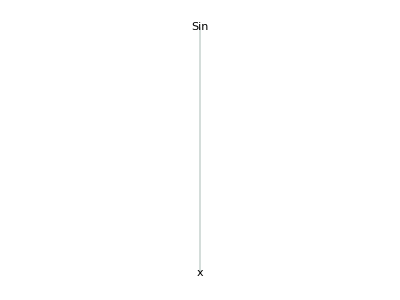
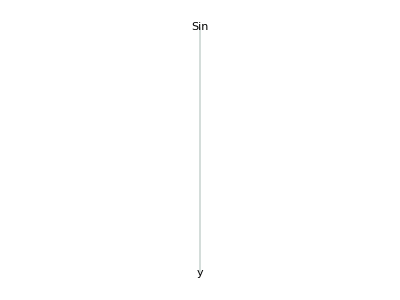

#### Example 4:

```mathematica
ExpressionDifference[{},{"a","b"}]
```

{Insert[{a,b},1]}

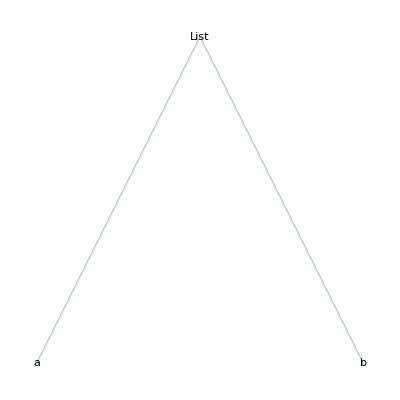
```mathematica
-Graphics--Graphics-
```

#### Example 5:

```mathematica
ExpressionDifference[{1,2,3},{1,"a",2,"b",3}]
```

{Insert[{a},2],Insert[{b},4]}

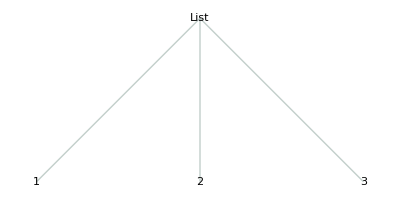
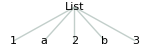

#### Example 6:

```mathematica
ExpressionDifference[sin["x"],cos["y"]]
```

{{Replace[_→cos]},ReplacePart[1→y]}

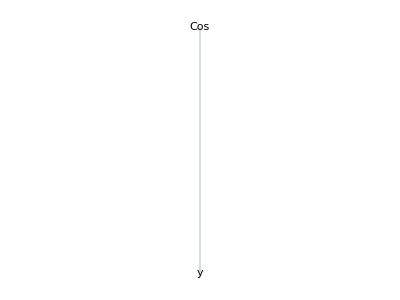
```mathematica
-Graphics--Graphics-
```

#### Example 7:

```mathematica
ExpressionDifference[f[x,y],g[x]]
```

{{Replace[_→g]},Delete[2]}

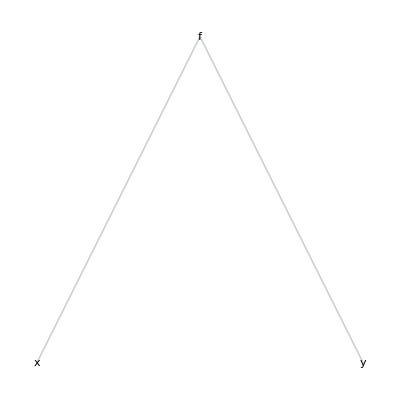
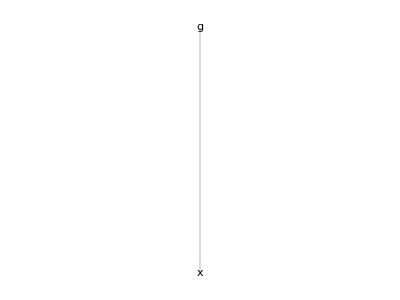

#### Example 8:

```mathematica
ExpressionDifference[Plus[Log[3x+y],5],Times[100,Times[x,2]]]
```

{{Replace[_→Times]},ReplacePart[1→200],ReplacePart[2→x]}

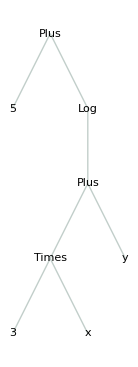
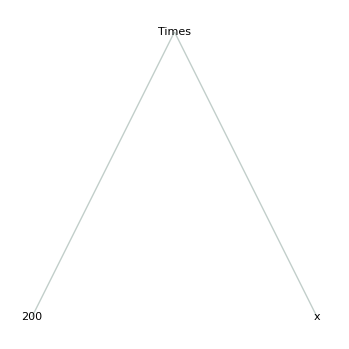

#### Example 9:

```mathematica
ExpressionDifference[{{1},{2}},{{{1},{2}}}]
```

{ReplacePart[1→{{1},{2}}],Delete[2]}

```mathematica
-Graphics-           -Graphics-
```

#### Example 10:

```mathematica
ExpressionDifference[Table[RandomInteger[10],10],Characters["Aman Connor"]]
```

{ReplacePart[1→A],ReplacePart[2→m],ReplacePart[3→a],ReplacePart[4→n],ReplacePart[5→ ],ReplacePart[6→C],ReplacePart[7→o],ReplacePart[8→n],ReplacePart[9→n],ReplacePart[10→o],Insert[r,11]}

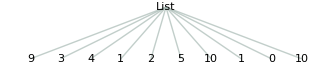
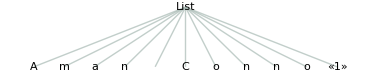

#### Example 11:

```mathematica
ExpressionDifference[Characters["Aman Dewangan"],Characters["Aman Connor"]]
```

{ReplacePart[6→C],ReplacePart[7→o],Delete[8],Delete[8],ReplacePart[9→n],ReplacePart[10→o],ReplacePart[11→r]}

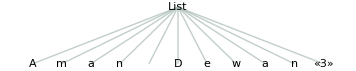
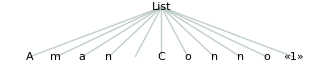

#### Example 12:

```mathematica
ExpressionDifference[MoleculePlot3D[Entity["Chemical","Methane"]],GeoGraphics[Entity["City",{"Raipur","Chhattisgarh","India"}]]]
```

{{Replace[_→GeoGraphics]},ReplacePart[1→-Graphics-],ReplacePart[2→GeoBackground→Automatic],ReplacePart[3→GeoCenter→GeoPosition[{21.24,81.63}]],ReplacePart[4→GeoGridLines→None],ReplacePart[5→GeoGridLinesStyle→GrayLevel[0.4, 0.3]],Insert[GeoGridRange→{{81.4536,81.8064},{21.5666,21.9214}},6],Insert[GeoGridRangePadding→None,7],Insert[GeoModel→ITRF00,8],Insert[GeoProjection→Mercator,9],Insert[GeoRange→{{21.0747,21.4053},{81.4536,81.8064}},10],Insert[GeoRangePadding→Full,11],Insert[GeoResolution→Automatic,12],Insert[GeoServer→{Automatic},13],Insert[GeoZoomLevel→11,14],Insert[MetaInformation→{GeoModel→ITRF00,LonLatBox→{{81.4536,81.8064},{21.0747,21.4053}},PlotRange→{{81.4533,81.8069},{21.5662,21.9218}},Projection→Mercator,Software→Created with the Wolfram Language: www.wolfram.com,TileSources→Wolfram Knowledgebase with data from © OpenStreetMap contributors: http://www.openstreetmap.org/copyright},15]}

#### Example 13:

```mathematica
ExpressionDifference[f["x","y","z"],f["a","b"]]
```

{ReplacePart[1→a],ReplacePart[2→b],Delete[3]}

```mathematica
-Graphics-           -Graphics-
```

#### Example 14:

```mathematica
ExpressionDifference[f["a","b"],f["x","y","z","h"]]
```

{ReplacePart[1→x],ReplacePart[2→y],Insert[z,3],Insert[h,4]}

```mathematica
-Graphics-           -Graphics-
```

#### Example 15:

```mathematica
ExpressionDifference[foo[{1,2}],foo[{1,2,3}]]
```

{ReplacePart[1→{1,2,3}]}

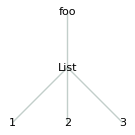
```mathematica
-Graphics-         -Graphics-
```

## Possible Issues:

Applying ExpressionDifference on Large Expressions may not work :

#### Case 1(Fails for Long Expression which involve Recursive Implementation) :

```mathematica
s1 = Hold@Replace[{expr1,expr2},{ (*Evaluating the Sequence "seq" using SequenceAlignment Operation on the given expression depending upon the DelayedRule of Matching Condition.*)
{xHead_[xe___],yHead_[ye___]}:> If[xHead===yHead,
count++;
SequenceAlignment[{xe},{ye}]
,
AppendTo[diff,ExpressionDifference[xHead,yHead]];
count++;
SequenceAlignment[{xe},{ye}]
]
}];

s2 = Hold@ReplacePart[{expr1,expr2},{ (*Evaluating the Sequence "seq" using SequenceAlignment Operation on the given expression depending upon the DelayedRule of Matching Condition.*)
{xHead_[xe___],yHead_[ye___]}:> If[xHead===yHead,
count++;
SequenceAlignment[{xe},{ye}]
,
AppendTo[diff,ExpressionDifference[xHead,yHead]];
count++;
Sequence[{xe},{ye}]
]
}];

ExpressionDifference[s1,s2]
```

AppendTo::rvalue: diff is not a variable with a value, so its value cannot be changed.

Increment::rvalue: count is not a variable with a value, so its value cannot be changed.

{ReplacePart[1→{ye}]}

#### Case 2 (Partially Wrong Output in some cases):

```mathematica
ExpressionDifference[Table[RandomInteger[x],{x,10,20,1}],Integrate[x^2+1,x]]
```

{{Replace[_→Plus]},ReplacePart[1→x],ReplacePart[2→x^3/3],Delete[3],Delete[3],Delete[3],Delete[3],Delete[3],Delete[3],Delete[3],Delete[3],Delete[3]}

## Concluding remarks

This version of ExpressionDifference fails to deal with cases figuring out the difference in the long expressions which involve recursive implementation of ExpressionDifferecne though it completely works fine for shorter expressions, and hence the recursive case still needs to be worked upon.

For text, it’s comparatively straightforward to find and indicate minimal changes. The idea is to develop an approach that involves figuring out how to do this for general symbolic expressions and figure out which changes can automatically be merged in a 3-way merge process.

The Minimum Tree Distance Approach is one of the possible ways to solve the problem, where we figure out the minimum number of operations that we need to perform on any expression “expr1” to convert it into “expr2”. In this way, we could figure out the number of changes, and then we can perform operations like Insert, ReplacePart and Delete accordingly on the given expressions.

Another approach involves Hashing of the expression tree and its branches and comparing the hash obtained for each branch with another expression to realize what’s the difference in the trees and accordingly suggest the necessary changes to the given expression.

The Future Scope of this Project involves developing with Functions like “DifferenceApply”  and “DifferenceVisualize”. “DifferenceApply” would apply a List of differences to expression “expr1” to convert it into another expression “expr2” and “DifferenceVisualize” would show what’s different between the two expressions.

## Keywords

Tree Difference

Tree Diffing

Difference

ExpressionTree

SequenceAlignment

ExpressionDifference

## Acknowledgment

Connor Gray(Mentor)

Carlos Muñoz (TA)

Silvia Hao (TA)

## References

https://thume.ca/2017/06/17/tree-diffing/

https://evolution.gs.washington.edu/phylip/doc/treedist.html

http://reference.wolfram.com/language/guide/Expressions.html

http://reference.wolfram.com/language/ref/EditDistance.html

http://reference.wolfram.com/language/ref/Inactivate.html